```mathematica
n= 10
```

10

```mathematica
Func = x^n * E^(-x)
```

ⅇ^-x x^10

```mathematica
y = x-n
```

-10+x

```mathematica
GaussApprox =  x^n * E^(-x)*E^(-y^2 / (2*n))
```

ⅇ^(-1/20 (-10+x)^2-x) x^10

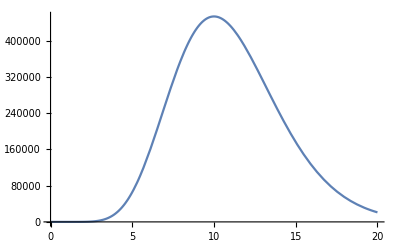

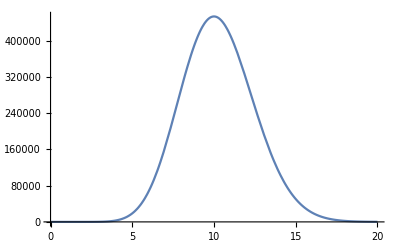

```mathematica
a = Plot[Func, {x,0,2n}]
b =Plot[GaussApprox, {x, 0, 2n}]
```

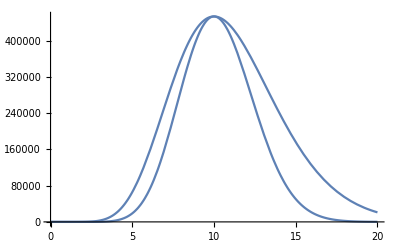

```mathematica
Show[a, b]
```